```mathematica
σ=1;
f[x_,x0_]:=(x-x0) Exp[-(x-x0)^2/(2 σ^2)]
g[x_,x0_]:=Exp[-(x-x0)^2/(2 σ^2)]
```

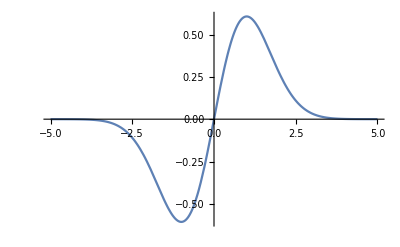

```mathematica
Plot[f[x,0],{x,-5,5}]
```

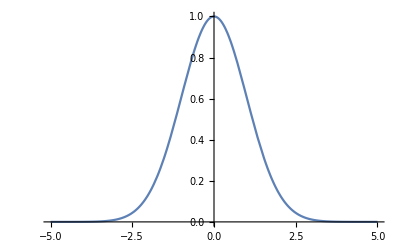

```mathematica
Plot[g[x,0],{x,-5,5}]
```

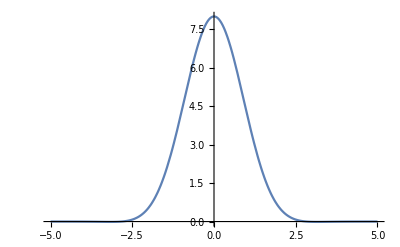

```mathematica
h[x_,x0_]:=8g[x,x0]-f[x,x0]
Plot[h[x,0],{x,-5,5}]
```